```mathematica
Integrate[Exp[2n p(1-p)],{p,1/2,pp}]
```

(ⅇ^(n/2) √(π/2) Erf[(√n (-1+2 pp))/(√2)])/(2 √n)

```mathematica
Erf[1/2 √2 (-1)]Exp[1/2]Sqrt[Pi/2]//N
```

-1.41069

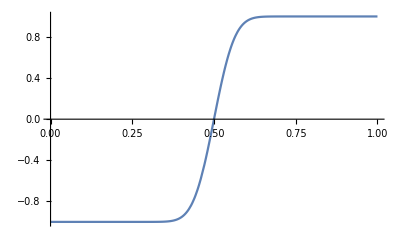

```mathematica
Plot[Erf[Sqrt[100/2] (-1+2 p)],{p,0,1}]
```

```mathematica
D[Erf[(-1+2p)Sqrt[n]/Sqrt[2]],p]
```

2 ⅇ^(-1/2 n (-1+2 p)^2) √n √(2/π)

```mathematica
step[k_,n_]:=If[k==0||k==n,k,If[Random[]>k/n,k-1,k+1]]
laststep[k_,n_]:=If[k==0||k==n,k,laststep[step[k,n],n]]
```

```mathematica
Tally[laststep[45,100]&/@Range[1000]]
```

{{0,841},{100,159}}

```mathematica
winprob[k_,n_]:=1/2.(1+Erf[(-1+2(k/n))Sqrt[n/2]]/Erf[Sqrt[n/2]])
```

```mathematica
winprob[45,100]
```

0.158655

```mathematica
winprob[21,51]
```

0.103789

```mathematica
n(1/2+1/(2Sqrt[n]))
```

(1/2+1/(2 √n)) n

```mathematica
winprob[60,100]-winprob[40,100]
```

0.9545

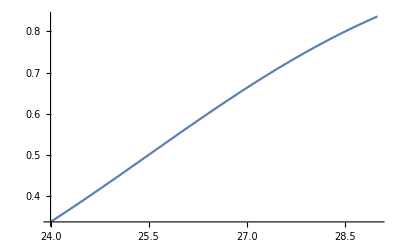

```mathematica
Plot[winprob[n,51],{n,24,29}]
```

```mathematica
winprob[64,63+31+8+8]
```

0.95694

```mathematica
%/(1-%)
```

22.2236